```mathematica
α=2.;u0=1.*10^-8;
k:=√(2e);
```

```mathematica
δ50Lepage={-0.000421343353,-0.133227246,-1.319383451,-0.900186195,-0.146570028,-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967};
```

```mathematica
δ50[V_]:=
Module[{r1=50,r2=u0,sol01,sol02,sol03,sol04,sol05,sol1,sol2,sol3,sol4,sol5,sol6,sol7,δ01,δ02,δ03,δ04,δ05,δ1,δ2,δ3,δ4,δ5,δ6,δ7,δs01,δs02,δs03,δs04,δs05,δs1,δs2,δs3,δs4,δs5,δs6,δs7},
e=10^-10;
sol01=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs01=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol01,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δ01=δ/.δs01;
δ01=NestWhile[Sign[#](Abs[#]-π)&,δ01,Abs[#]>π/2&];
e=10^-5;
sol02=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs02=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol02,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δ02=δ/.δs02;
δ02=NestWhile[Sign[#](Abs[#]-π)&,δ02,Abs[#]>π/2&];
e=0.001;
sol03=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs03=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol03,{δ,-1.3},WorkingPrecision->20];
δ03=δ/.δs03;
δ03=NestWhile[Sign[#](Abs[#]-π)&,δ03,Abs[#]>π/2&];
e=0.003;
sol04=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs04=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol04,{δ,-1.3},WorkingPrecision->20];
δ04=δ/.δs04;
δ04=NestWhile[Sign[#](Abs[#]-π)&,δ04,Abs[#]>π/2&];
e=0.007;
sol05=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs05=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol05,{δ,-1.3},WorkingPrecision->20];
δ05=δ/.δs05;
δ05=NestWhile[Sign[#](Abs[#]-π)&,δ05,Abs[#]>π/2&];
e=0.01;
sol1=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-1.3},WorkingPrecision->20];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
e=0.03;
sol2=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,0.9},WorkingPrecision->20];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
e=0.07;
sol3=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.2},WorkingPrecision->20];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
e=0.1;
sol4=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.6},WorkingPrecision->20];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
e=0.3;
sol5=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs5=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol5,{δ,1.2},WorkingPrecision->20];
δ5=δ/.δs5;
δ5=NestWhile[Sign[#](Abs[#]-π)&,δ5,Abs[#]>π/2&];
e=0.7;
sol6=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs6=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol6,{δ,-0.6},WorkingPrecision->20];
δ6=δ/.δs6;
δ6=NestWhile[Sign[#](Abs[#]-π)&,δ6,Abs[#]>π/2&];
e=1;
sol7=Flatten@NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs7=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol7,{δ,-1.1},WorkingPrecision->20];
δ7=δ/.δs7;
δ7=NestWhile[Sign[#](Abs[#]-π)&,δ7,Abs[#]>π/2&];
{δ01,δ02,δ03,δ04,δ05,δ1,δ2,δ3,δ4,δ5,δ6,δ7}
]
```

```mathematica
δ501=δ50[-1.3862179318475605/#^1.2152447118079408&];
δ502=δ50[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&];
δ503=δ50[-0.39300593613292306/#^1.5993730406518318-1/#&];
δ504=δ50[-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&];
N[{δ501,δ502,δ503,δ504},6]//TableForm
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (-1.15531775788807669651212551510632501212584802323==0.491935 Cot[35.7294+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (0.690857047678012871843562992335232029596491483797==0.335659 Cot[30.3019+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (0.136368115165502889076239311409220396197582667944==0.287352 Cot[26.7983+δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (-0.0050548676284763871906775968288150267415083678453==0.491935 Cot[35.7294+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.0790497090489487333225391318363253476866298078556==0.335659 Cot[30.3019+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.352410573588944237735496186915957915248473388101==0.287352 Cot[26.7983+δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+0.393006 Power[«2»]+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (-0.332577381045120221187158279739374250617335448516==0.491935 Cot[35.7294+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.890456450734191329766867214564530484868371608457==0.335659 Cot[30.3019+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (0.615681208021622189967792395078525489185325941998==0.287352 Cot[26.7983+δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+0.793895 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (0.0268900142680018751243161717258922777229867462117==0.491935 Cot[35.7294+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.0426361837463542776266323409931347972761878052597==0.335659 Cot[30.3019+δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.254405400146293142211832623489437541117592745752==0.287352 Cot[26.7983+δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

-0.0846239 | -0.82672 | 1.56719 | 1.56633 | -0.537888 | 0.825659 | 1.16656 | -0.427518 | 0.0141856 | 0.801057 | 0.970408 | 0.974231
-0.0849526 | -0.93085 | 0.409218 | -0.225442 | 0.791948 | -0.821411 | -0.78699 | 0.525591 | 0.841445 | 1.26387 | 1.24433 | 1.18786
-0.0847698 | -0.873049 | 0.99342 | 0.753583 | -1.22892 | 0.191835 | 0.115401 | 1.3296 | -1.52868 | -1.22772 | -1.34313 | -1.43724
-0.0849755 | -0.938083 | 0.344335 | -0.330388 | 0.629865 | -0.998193 | -0.940985 | 0.377673 | 0.696108 | 1.13346 | 1.13079 | 1.08237

```mathematica
{(δ501-δ50Lepage),(δ502-δ50Lepage),(δ503-δ50Lepage),(δ504-δ50Lepage)}//TableForm
```

-0.0842026 | -0.693492 | 2.88657 | 2.46652 | -0.391318 | 1.48049 | -0.0663082 | 0.152102 | 1.17063 | 0.907523 | 2.42783 | -0.186404
-0.0845313 | -0.797623 | 1.7286 | 0.674744 | 0.938518 | -0.166575 | -2.01986 | 1.10521 | 1.99789 | 1.37033 | 2.70175 | 0.0272289
-0.0843485 | -0.739822 | 2.3128 | 1.65377 | -1.08235 | 0.84667 | -1.11747 | 1.90922 | -0.372239 | -1.12125 | 0.114296 | -2.59788
-0.0845542 | -0.804856 | 1.66372 | 0.569798 | 0.776435 | -0.343357 | -2.17385 | 0.957293 | 1.85255 | 1.23993 | 2.58821 | -0.0782638

```mathematica
{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage)}//TableForm
```

-0.0842026 | -0.693492 | -0.255019 | -0.675073 | -0.391318 | 1.48049 | -0.0663082 | 0.152102 | 1.17063 | 0.907523 | -0.713758 | -0.186404
-0.0845313 | -0.797623 | -1.41299 | 0.674744 | 0.938518 | -0.166575 | 1.12174 | 1.10521 | -1.1437 | 1.37033 | -0.43984 | 0.0272289
-0.0843485 | -0.739822 | -0.828789 | -1.48782 | -1.08235 | 0.84667 | -1.11747 | -1.23237 | -0.372239 | -1.12125 | 0.114296 | 0.543717
-0.0845542 | -0.804856 | -1.47787 | 0.569798 | 0.776435 | -0.343357 | 0.96774 | 0.957293 | -1.28904 | 1.23993 | -0.553378 | -0.0782638

```mathematica
Abs@{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage)}//TableForm
Mean@#&/@%
```

0.0842026 | 0.693492 | 0.255019 | 0.675073 | 0.391318 | 1.48049 | 0.0663082 | 0.152102 | 1.17063 | 0.907523 | 0.713758 | 0.186404
0.0845313 | 0.797623 | 1.41299 | 0.674744 | 0.938518 | 0.166575 | 1.12174 | 1.10521 | 1.1437 | 1.37033 | 0.43984 | 0.0272289
0.0843485 | 0.739822 | 0.828789 | 1.48782 | 1.08235 | 0.84667 | 1.11747 | 1.23237 | 0.372239 | 1.12125 | 0.114296 | 0.543717
0.0845542 | 0.804856 | 1.47787 | 0.569798 | 0.776435 | 0.343357 | 0.96774 | 0.957293 | 1.28904 | 1.23993 | 0.553378 | 0.0782638

{0.564694,0.773586,0.797595,0.761877}

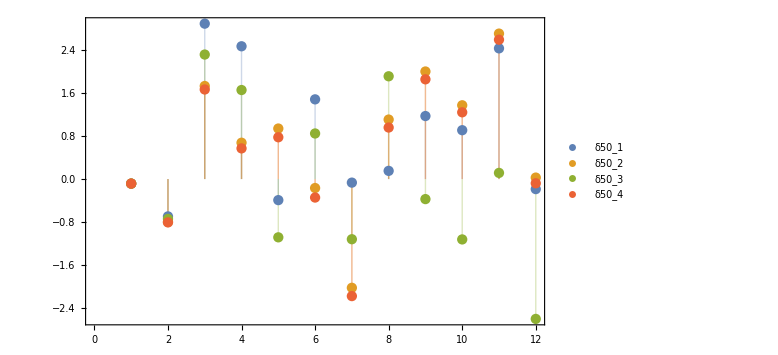

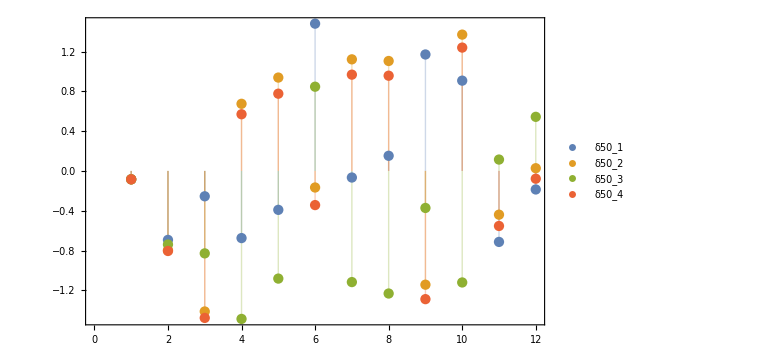

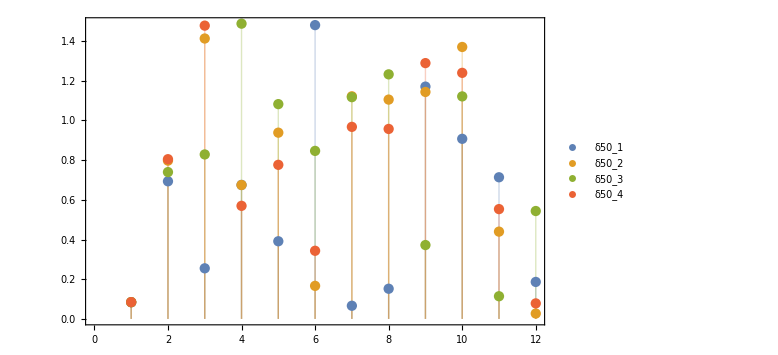

```mathematica
ListPlot[{(δ501-δ50Lepage),(δ502-δ50Lepage),(δ503-δ50Lepage),(δ504-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{"δ50_1","δ50_2","δ50_3","δ50_4"},Joined->False]
ListPlot[{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{"δ50_1","δ50_2","δ50_3","δ50_4"},Joined->False]
ListPlot[Abs@{NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ501-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ502-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ503-δ50Lepage),NestWhile[Sign[#](Abs[#]-π)&,#,Abs[#]>π/2&]&/@(δ504-δ50Lepage)},Filling->Axis,Frame->True,ImageSize->Large,PlotLegends->{"δ50_1","δ50_2","δ50_3","δ50_4"},Joined->False]
```